```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab10\lab10\lab10

```mathematica
test1lim1 =Import["test1_limit1.txt","List"];
test1lim2 = Import["test1_limit2.txt","List"];
test2lim1 = Import["test2_limit1.txt","List"];
test2lim2 = Import["test2_limit2.txt","List"];
```

```mathematica
Length@test1lim1
```

201

```mathematica
points1 = Table[{i/(Length@test1lim1 - 1),test1lim1[[i]]},{i,0, Length@test1lim1-1}];
points1lim2 = Table[{0.1 +0.9i/(Length@test1lim2 - 1),test1lim2[[i]]},{i,0, Length@test1lim2-1}];
points2 = Table[{i/(Length@test2lim1 - 1),test2lim1[[i]]},{i,0, Length@test2lim1-1}];
points2lim2 = Table[{0.1 +0.9i/(Length@test1lim2 - 1),test2lim2[[i]]},{i,0, Length@test2lim2-1}];
```

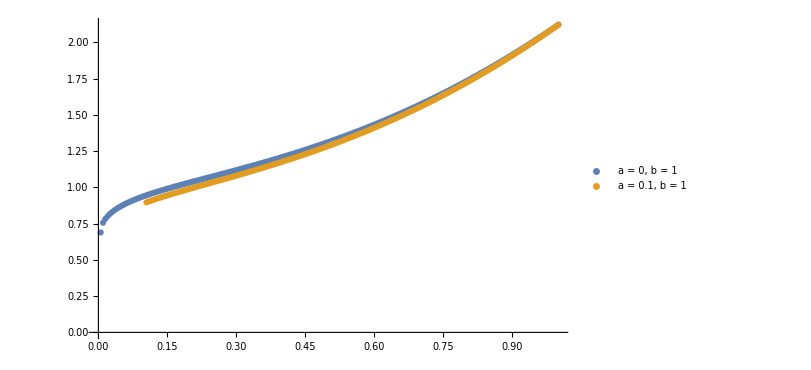

```mathematica
g = ListPlot[{points2, points2lim2},ImageSize->600,PlotLegends->{"a = 0, b = 1", "a = 0.1, b = 1"}]
```

```mathematica
Export["test2_SIM.jpg", g]
```

test2_SIM.jpg